```mathematica
(*cell cycle 45 variables model: with check point*)
```

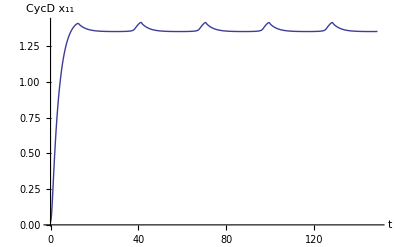

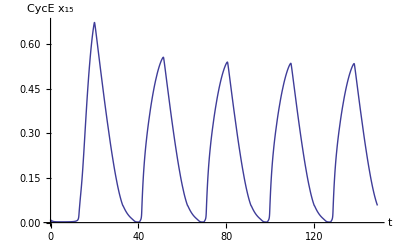

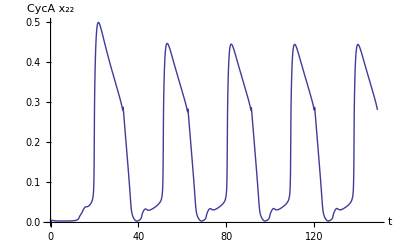

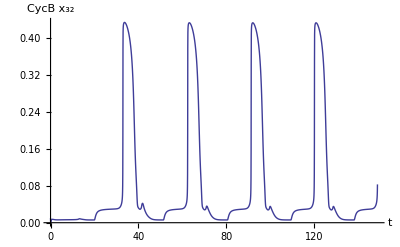

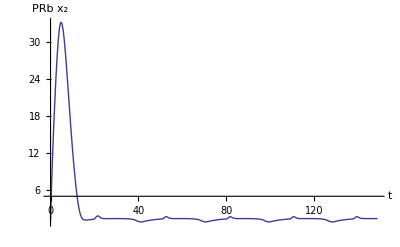

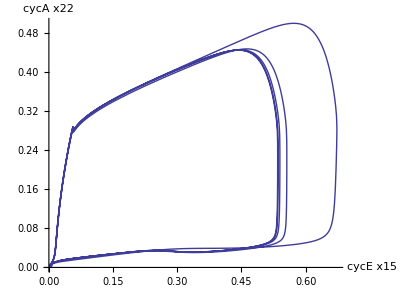

28.9

0.535649

60

28.9

0.524659

60

28.9

0.501689

60

29.

0.422512

60

```mathematica
(*d=0.05;*)
d=0.001;
n=44;

(****) 
(*Mitotic stimulation by growth factor,GF*)
GF = 1;Kagf =0.1;kdap1 =0.15;eps = 17;vsap1 =1;
(*Antagonistic regulation exerted by pRB and E2F*)
kde2f =0.002;kde2fp = 1.1; kdprb = 0.01; kdpRBp = 0.06(*kdprbp in tableS2*); kdpRBpp = 0.04(*kdprbpp in tableS2*); 
kpc1 = 0.05;kpc2 =0.5;kpc3 =0.025;kpc4 =0.5;
K1 = 0.1 ;K2 = 0.1 ;K3 = 0.1;K4 = 0.1 ;
V1 = 2.2;V2 = 2;V3 = 1;V4 = 2;
K1e2f =5 ;K2e2f = 5 ;V1e2f =4;V2e2f = 0.75 ;vse2f =0.15 ;vsprb = 0.8 ;
(*Module Cyclin D/Cdk4-6:G1 phase*)
Cdk4tot = 1.5 ;Ki7 = 0.1 ;Ki8 = 2 ;kcd1 =0.4 ;kcd2 = 0.005 ;
kdecom1 =0.1 ;kcom1 = 0.175 ;kc1 =0.15 ;kc2 =0.05 ;
kddd =0.005 ;Kdd = 0.1 ;K1d = 0.1 ;K2d = 0.1 ;Vdd =5;Vm1d = 1;Vm2d = 0.2;
(*Module Cyclin E/Cdk2:G1 phase and transition G1/S*)
ae =0.25;Cdk2tot = 2;ib1 =0.5;Ki9 = 0.1;Ki10 = 2;kce = 0.29(*0.29,0.24 for with ATR check point*);
kc3 = 0.2 ;kc4 =0.1 ;kdecom2 =0.1 ;kcom2 = 0.2 ;kdde =0.005 ;kddskp2 =0.005 ;
kdpe =0.075 ;kdpei =0.15 ;Kde = 0.1 ;Kdceskp2 =2 ;Kdskp2 =0.5 ;Kcdh1 =0.4 ;
K1e =0.1 ;K2e =0.1 ;K5e =0.1 ;K6e = 0.1 ;Vde =3 ;Vdskp2 = 1.1 ;
Vm1e =2 ;Vm2e =1.4 ;Vm5e =5 ;V6e =0.8 ;vspei =0.13 ;vsskp2 = 0.15 ;
xe1 =1;xe2 =1;
(*Module Cyclin A/Cdk2:S phase and transition S/G2*)
aax=0.2 ;ib2 =0.5 ;Ki11 =0.1 ;Ki12 = 2 ;Ki13 = 0.1 ;Ki14 = 2 ;
kca = 0.0375 ;kdecom3 =0.1 ;kcom3 = 0.2 ;
kc5 =0.15 ;kc6 =0.125 ;kdda =0.005 ;kddp27 =0.06 ;kddp27p =0.01 ;
kdcdh1a =0.1 ;kdcdh1i =0.2 ;kdpa =0.075 ;kdpai =0.15 ;Kda = 1.1 ;Kdp27p = 0.1 ;
Kdp27skp2=0.1 ;Kacdc20 =2 ;
K1a =0.1 ;K2a =0.1 ;K1cdh1 =0.01 ;K2cdh1 =0.01 ;
K5a =0.1 ;K6a = 0.1 ;K1p27 = 0.5 ;K2p27 = 0.5 ;Vdp27p = 5 ;
Vda = 2.5 ;Vm1a =2 ;Vm2a =1.85 ;Vm5a =4 ;V6a = 1;vscdh1a=0.11;vspai =0.105 ;
vs1p27 = 0.8 ;vs2p27 = 0.1 ;V1cdh1 =1.25 ;V2cdh1 =8 ;V1p27 =100 ;V2p27 =0.1 ;
xa1 =1;xa2 =1;
(*Module Cyclin B/Cdk1:G2 phase and transition G2/M*)
ab =0.11 ;Cdk1tot = 0.5 ;
ib =0.75 ;ib3 =0.5 ;kc7 =0.12 ;kc8 =0.2;kdecom4 =0.1 ;kcom4 = 0.25 ;
kdcdc20a =0.05 ;kdcdc20i =0.14 ;kddb =0.005 ;kdpb =0.1 ;kdpbi =0.2 ;
kdwee1 =0.1 ;kdwee1p =0.2 ;Kdb = 0.005 ;Kdbcdc20 =0.2 ;Kdbcdh1 =0.1;
ksw =5 ;K1b =0.1 ;K2b =0.1 ;K3b =0.1 ;K4b =0.1 ;K5b =0.1 ;K6b = 0.1 ;K7b =0.1 ;K8b =0.1 ;vcb = 0.05 ;Vdb = 0.06 ;Vm1b =3.9 ;Vm2b =2.1 ;
vscdc20i =0.1 ; Vm3b=8; Vm4b =0.7 ;Vm5b =5 ;V6b = 1 ;Vm7b =1.2 ;Vm8b =1 ;vspbi =0.12 ;vswee1 =0.06 ;xb1 =1;xb2 =1; 

(*Additional parameters The ATR/Chk1 DNA replication checkpoint*)
ATRtot = 0.5 ;Chk1tot = 0.5 ;Cdc45tot = 0.5 ;
kaatr =0.022;(*kaatr =0.022 with ATR/Chk1 check point, 0 without check point;*)
(*kaatr=0;*)
kdatr =0.15 ;kdpol =0.2 ;
kdprim =0.15 ;kspol =0.8 ;ksprim =0.05 ;K1cdc45 =0.02 ;K2cdc45 =0.02 ;
K1chk =0.5 ;K2chk =0.5 ;Poltot = 0.5 ;V1cdc45 =0.8 ;V2cdc45 =0.12 ;V1chk =4 ;V2chk =0.1 ;

(*Coupling the mammalian cell cycle to the circadian clock*)
Kdw = 0.5 ;Kiw =1 ;nc =4;vdw = 0.5;vsw = 0 ; (*vsw=0.2 with coupling*)

(**circ1**)
(*kce=0; vs1p27=0;vs2p27=0;vcb=0; vse2f=0.025;*)
(**circ2**)
(*vcb=0;V1e2f=0;*)
(**circ3**)
(*V1e2f=0;kce=0;vs1p27=0;vs2p27=0;Vdb=0.5;Kdbcdh1=0.01;*)
(**circ4**)
(*V1e2f=0;kce=0;vs1p27=0;vs2p27=0;Vda=0.1;Kdbcdc20=0.1;*)

kks=0;
(*GF=2;*)
sm=0.1;
If[kks==1,vsap1=vsap1*(1+sm)];
If[kks==2,vse2f=vse2f*(1+sm)];
If[kks==3,vsprb=vsprb*(1+sm)];
If[kks==4,vspei=vspei*(1+sm)];(*cdc25,n*)
If[kks==5,vsskp2=vsskp2*(1+sm)];
If[kks==6,vscdh1a=vscdh1a*(1+sm)];(*cdh1*)
If[kks==7,vspai=vspai*(1+sm)]; (*cdc25,n*)
If[kks==8,vs1p27=vs1p27*(1+sm)];
If[kks==9,vs2p27=vs2p27*(1+sm)];
If[kks==10,vcb=vcb*(1+sm)];
If[kks==11,vscdc20i=vscdc20i*(1+sm)]; (*cdc20*)
If[kks==12,vspbi=vspbi*(1+sm)];(*cdc25,n*)
If[kks==13,vswee1=vswee1*(1+sm)];(**wee1,n*)

If[kks==14,kcd1=kcd1*(1+sm)]; (**CycD induced by AP1**)
If[kks==15,kcd2=kcd2*(1+sm)]; (**CycD induced by E2F**)
If[kks==16,kcom1=kcom1*(1+sm)];(**CycD bind Cdk4,6**)
If[kks==17,kc1=kc1*(1+sm)]; (**CycD/Cdk4,6 bind p27**)
If[kks==18,kce=kce*(1+sm)];(**CycE synthesis induced by E2F**)
If[kks==19,kc3=kc3*(1+sm)];(**CycE/Cdk2 bind p27**)
If[kks==20,kcom2=kcom2*(1+sm)]; (**CycE bind Cdk2**)
If[kks==21,kcom3=kcom3*(1+sm)];(**CycA bind Cdk2**)
If[kks==22,kc5=kc5*(1+sm)];(**CycA/Cdk2 bind p27**)
If[kks==23,kc7=kc7*(1+sm)];(**CycB/Cdk1 bind p27**)
If[kks==24,kcom4=kcom4*(1+sm)];(**CycB bind Cdk1**)

(****)
AP1=Subscript[x, 1][t];
pRB=Subscript[x, 2][t];
pRBc1=Subscript[x, 3][t];
pRBp=Subscript[x, 4][t];
pRBc2=Subscript[x, 5][t];
pRBpp=Subscript[x, 6][t];
E2F=Subscript[x, 7][t];
E2Fp=Subscript[x, 8][t];
Cd=Subscript[x, 9][t];(*cycD*)
Mdi=Subscript[x, 10][t];
Md=Subscript[x, 11][t]; (*Active complex cyclin D/Cdk4-6*)
Mdp27=Subscript[x, 12][t];
Ce=Subscript[x, 13][t];(*cycE*)
Mei=Subscript[x, 14][t];
Me=Subscript[x, 15][t]; (*Active complex cyclin E/Cdk2*)
Skp2=Subscript[x, 16][t];
Mep27=Subscript[x, 17][t];
Pei=Subscript[x, 18][t];
Pe=Subscript[x, 19][t];
Ca=Subscript[x, 20][t];(*cycA*)
Mai=Subscript[x, 21][t];
Ma=Subscript[x, 22][t]; (*Active complex cyclin A/Cdk2*)
Map27=Subscript[x, 23][t];
p27=Subscript[x, 24][t];
p27p=Subscript[x, 25][t];
Cdh1i=Subscript[x, 26][t];
Cdh1a=Subscript[x, 27][t];
Pai=Subscript[x, 28][t];
Pa=Subscript[x, 29][t];
Cb=Subscript[x, 30][t];(*cycB*)
Mbi=Subscript[x, 31][t];
Mb=Subscript[x, 32][t];(*Active complex cyclin B/Cdk1*)
Mbp27=Subscript[x, 33][t];
Cdc20i=Subscript[x, 34][t];
Cdc20a=Subscript[x, 35][t];
Pbi=Subscript[x, 36][t];
Pb=Subscript[x, 37][t];
Wee1=Subscript[x, 38][t];
Wee1p=Subscript[x, 39][t];
Cdc45=Subscript[x, 40][t];
Pol=Subscript[x, 41][t];(*Pol alpha*)
Primer=Subscript[x, 42][t];
ATR=Subscript[x, 43][t];(*ATR*)
Chk1=Subscript[x, 44][t];
(*Mw=Subscript[x, 45][t];*)
Mw=0;

(************************************)
Subscript[F, 1]=(vsap1* (GF/(Kagf + GF))-kdap1 *AP1) * eps;
Subscript[F, 2]=(vsprb- kpc1 * pRB* E2F + kpc2 * pRBc1-V1 * (pRB/( K1+pRB)) * (Md+Mdp27)+V2*(pRBp/( K2+pRBp)) - kdprb * pRB) * eps;
Subscript[F, 3]=(kpc1*pRB*E2F-kpc2*pRBc1)*eps;
Subscript[F, 4] =(V1 *(pRB/(K1 + pRB)) * (Md+Mdp27) -V2 * (pRBp/(K2 + pRBp))-V3 * (pRBp/( K3+pRBp)) * Me +V4 * (pRBpp/( K4+pRBpp)) - kpc3 * pRBp* E2F+kpc4 * pRBc2 - kdpRBp * pRBp) * eps;
Subscript[F, 5]=(kpc3 * pRBp* E2F -kpc4 * pRBc2) * eps;
 Subscript[F, 6]=(V3 * (pRBp/(K3 + pRBp)) * Me -V4 * (pRBpp/(K4 + pRBpp)) - kdpRBpp * pRBpp)*eps;
Subscript[F, 7]=(vse2f - kpc1 * pRB* E2F+kpc2 * pRBc1- kpc3 * pRBp* E2F + kpc4 * pRBc2
-V1e2f * Ma* (E2F/( K1e2f+E2F))+V2e2f * (E2Fp/( K2e2f+E2Fp)) - kde2f * E2F) * eps;
Subscript[F, 8]= (V1e2f * Ma* (E2F/(K1e2f + E2F)) -V2e2f * (E2Fp/( K2e2f+E2Fp)) -kde2fp * E2Fp) * eps;
Subscript[F, 9]=(kcd1 * AP1+ kcd2 * E2F * (Ki7/(Ki7 + pRB)) * (Ki8/( Ki8+pRBp)) -kcom1 * Cd * (Cdk4tot - (Mdi+Md+Mdp27))+kdecom1 * Mdi
-Vdd * (Cd/( Kdd+Cd)) - kddd * Cd) * eps;
Subscript[F, 10]=(kcom1 * Cd * (Cdk4tot - (Mdi+Md+Mdp27)) -kdecom1 * Mdi + Vm2d * (Md/( K2d+Md)) -Vm1d * (Mdi/(K1d + Mdi))) * eps;
Subscript[F, 11]=(Vm1d * (Mdi/(K1d + Mdi)) -Vm2d * (Md/( K2d+Md)) - kc1 * Md* p27+kc2 * Mdp27) * eps;
Subscript[F, 12]=(kc1 * Md* p27 - kc2 * Mdp27) * eps;

Subscript[F, 13]=(kce * E2F * (Ki9 /(Ki9+pRB)) * (Ki10/(Ki10 + pRBp))
-kcom2 * Ce * (Cdk2tot -(Mei + Me + Mep27 + Mai + Ma+ Map27))
+kdecom2 * Mei -Vde * (Skp2/(Kdceskp2 + Skp2)) * (Ce/( Kde+Ce)) - kdde * Ce) * eps;
Subscript[F, 14]=(kcom2 * Ce * (Cdk2tot - (Mei+Me+Mep27+Mai+Ma+Map27)) -kdecom2 * Mei +Vm2e * (Wee1+ib1) * (Me/(K2e + Me)) -Vm1e * Pe * (Mei/(K1e + Mei))) * eps;
 Subscript[F, 15]=(Vm1e * Pe * (Mei/( K1e+Mei)) -Vm2e * (Wee1+ ib1) * (Me/( K2e+Me)) -kc3 * Me* p27+kc4 * Mep27) * eps;

Subscript[F, 16]=(vsskp2 -Vdskp2 * (Skp2/(Kdskp2 + Skp2)) * (Cdh1a/(Kcdh1 + Cdh1a)) - kddskp2 * Skp2) * eps;

Subscript[F, 17]=(kc3 * Me* p27 - kc4 * Mep27) * eps;

Subscript[F, 18]=(vspei+V6e * (xe1 + xe2 * Chk1) * (Pe/(K6e + Pe))
-Vm5e * (Me+ae) * (Pei/(K5e + Pei)) - kdpei * Pei) * eps;

Subscript[F, 19]= (Vm5e * (Me+ae) * (Pei/(K5e + Pei))
-V6e * (xe1+xe2 * Chk1) * (Pe/( K6e+Pe)) - kdpe * Pe) * eps;


Subscript[F, 20]=(kca * E2F * (Ki11/( Ki11+pRB)) * (Ki12/(Ki12 + pRBp))
-kcom3 * Ca* (Cdk2tot - (Mei + Me + Mep27 + Mai + Ma+ Map27))
+kdecom3 * Mai -Vda * (Ca/(Kda + Ca)) * (Cdc20a/( Kacdc20+Cdc20a)) - kdda * Ca) * eps;

Subscript[F, 21]=(kcom3 * Ca* (Cdk2tot - (Mei+Me+Mep27+Mai+Ma+Map27)) -kdecom3 * Mai + Vm2a * (Wee1+ib2) * (Ma/(K2a + Ma)) -Vm1a * Pa* (Mai/(K1a + Mai))) * eps;

Subscript[F, 22]=(Vm1a * Pa* (Mai/( K1a+Mai)) -Vm2a * (Wee1+ ib2) * (Ma/( K2a+Ma)) -kc5 * Ma* p27+kc6 * Map27) * eps;

Subscript[F, 23]=(kc5 * Ma* p27 - kc6 * Map27) * eps;
Subscript[F, 24]=(vs1p27+vs2p27 * E2F * (Ki13/( Ki13+pRB)) * (Ki14/(Ki14 + pRBp)) - kc1 * Md * p27 + kc2 * Mdp27 -kc3 * Me* p27+kc4 * Mep27 - kc5 * Ma* p27 + kc6 * Map27 - kc7 * Mb* p27+kc8 * Mbp27 -V1p27 * Me* (p27/(K1p27 + p27)) + V2p27 * (p27p/( K2p27+p27p)) - kddp27 * p27) * eps;

Subscript[F, 25]=(V1p27 * Me* (p27/(K1p27+p27)) -V2p27 * (p27p/(K2p27 + p27p))
-Vdp27p * (Skp2/( Kdp27skp2+Skp2)) * (p27p/(Kdp27p + p27p)) - kddp27p * p27p) * eps;

Subscript[F, 26]= (V2cdh1 * (Cdh1a/( K2cdh1+Cdh1a)) * (Ma + Mb) -V1cdh1 * (Cdh1i/( K1cdh1+Cdh1i)) -kdcdh1i * Cdh1i) * eps;

Subscript[F, 27]=(vscdh1a+V1cdh1 * (Cdh1i/(K1cdh1 + Cdh1i)) -V2cdh1 * (Cdh1a/( K2cdh1+Cdh1a)) * (Ma + Mb)
-kdcdh1a * Cdh1a) * eps;

Subscript[F, 28]= (vspai + V6a * (xa1+xa2 * Chk1) * (Pa /(K6a+Pa)) -Vm5a * (Ma+ aax ) * (Pai/( K5a+Pai)) - kdpai * Pai) * eps; (**Subscript[a, a]->aax**)

Subscript[F, 29]=(Vm5a * (Ma + aax) * (Pai/( K5a+Pai)) -V6a * (xa1 + xa2 * Chk1) * (Pa/(K6a + Pa)) - kdpa * Pa) * eps;

Subscript[F, 30]= (vcb - kcom4 * Cb* (Cdk1tot - (Mbi + Mb+ Mbp27)) + kdecom4 * Mbi
-Vdb * (Cb/( Kdb+Cb)) *((Cdc20a/( Kdbcdc20+Cdc20a))+(Cdh1a/(Kdbcdh1+Cdh1a))) - kddb * Cb) * eps;

Subscript[F, 31]= (kcom4 * Cb* (Cdk1tot - (Mbi + Mb+ Mbp27)) - kdecom4 * Mbi+Vm2b * (Wee1+ ib3 ) * (Mb/( K2b+Mb)) -Vm1b * Pb* (Mbi/( K1b+Mbi))) * eps;
Subscript[F, 32]= (Vm1b * Pb* (Mbi/(K1b + Mbi)) -Vm2b * (Wee1+ib3) * (Mb/(K2b + Mb))-kc7 * Mb* p27 + kc8 * Mbp27) * eps;

Subscript[F, 33]= (kc7 * Mb* p27 - kc8 * Mbp27) * eps;
Subscript[F, 34]= (vscdc20i -Vm3b * Mb* (Cdc20i/( K3b+Cdc20i))+Vm4b * (Cdc20a/( K4b+Cdc20a))
-kdcdc20i * Cdc20i) * eps;

Subscript[F, 35]= (Vm3b * Mb* (Cdc20i/(K3b + Cdc20i)) -Vm4b * (Cdc20a/( K4b+Cdc20a))
-kdcdc20a * Cdc20a) * eps;

Subscript[F, 36]=(vspbi+V6b * (xb1 + xb2 * Chk1) * (Pb/(K6b + Pb))
-Vm5b * (Mb+ab) * (Pbi/(K5b + Pbi)) - kdpbi * Pbi) * eps;

Subscript[F, 37]= (Vm5b * (Mb+ab) * (Pbi/(K5b + Pbi))
-V6b * (xb1+xb2 * Chk1) * (Pb/( K6b+Pb)) - kdpb * Pb) * eps;

Subscript[F, 38]=(vswee1+ksw * Mw -Vm7b * (Mb+ib) * (Wee1/(K7b + Wee1))+Vm8b * (Wee1p/( K8b+Wee1p)) - kdwee1 *Wee1) * eps;

Subscript[F, 39]=(Vm7b * (Mb + ib ) * (Wee1/( K7b+Wee1)) -Vm8b * (Wee1p/(K8b + Wee1p))
-kdwee1p *Wee1p) * eps;

Subscript[F, 40]=(V1cdc45 * Me* ((Cdc45tot - Cdc45)/( K1cdc45+(Cdc45tot - Cdc45))) -V2cdc45 * (Cdc45/(K2cdc45 + Cdc45)) - kspol * (Poltot - Pol) * Cdc45 + kdpol * Pol) * eps;

Subscript[F, 41]= (kspol * (Poltot - Pol) * Cdc45 - kdpol * Pol) * eps;
 Subscript[F, 42]= (ksprim * Pol -kdprim * Primer-kaatr * (ATRtot - ATR) * Primer + kdatr * ATR) * eps;

Subscript[F, 43]= (kaatr * (ATRtot - ATR) * Primer - kdatr * ATR) * eps;
Subscript[F, 44]= (V1chk * ATR* ((Chk1tot - Chk1)/(K1chk + (Chk1tot -Chk1))) -V2chk * (Chk1/( K2chk+Chk1))) * eps;
(*Subscript[F, 45]=vsw * (Bn^nc/(Kiw^nc + Bn^nc)) - vdw * (Mw/( Kdw+Mw));*)
(*Subscript[F, 45]=0;*)

(**)
evaluating Off[General::spell1];
tmin=0;
tmax=150;
is=1;
ie=n;
rr=0.1;
xini={0.01,1,0.25,0.1,0.01,0.01,0.1,0.05,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.25,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.1,0.01,0.01,0.01,0.01,0.01,0.01};
(*xini=RandomReal[rr,n];*)

bini={0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01};

For[i=is,i≤ie,i++,
Subscript[eq, i]=Subscript[x, i]'[t]==Subscript[F, i];]
For[i=is,i≤ie,i++,
(*Subscript[eqb, i]=Subscript[b, i]'[t]==2*D[Subscript[F, i],Subscript[x, i][t]]*Subscript[b, i][t]+2*d*Subscript[x, i][t];*)
Subscript[eqb, i]=Subscript[b, i]'[t]==2*D[Subscript[F, i],Subscript[x, i][t]]*Subscript[b, i][t]+2*d;];
For[i=is,i≤ie,i++,
Subscript[xi, i]=Subscript[x, i][0]==xini[[i]];]
For[i=is,i≤ie,i++,
Subscript[bi, i]=Subscript[b, i][0]==bini[[i]];]
(**********************)
XT=Table[Subscript[x, i][t],{i,is,ie}];
BT=Table[Subscript[b, i][t],{i,is,ie}];
XTBT=Join[XT,BT];
EQ=Table[Subscript[eq, i],{i,is,ie}];
XI=Table[Subscript[xi, i],{i,is,ie}];
EQB=Table[Subscript[eqb, i],{i,is,ie}];
BI=Table[Subscript[bi, i],{i,is,ie}];
(*solve first and second moment*)
res=NDSolve[{EQ,XI,EQB,BI},XTBT,{t,tmin,tmax},MaxSteps->∞];
(*res=NDSolve[{EQ,XI},XT,{t,tmin,tmax},MaxSteps->∞];(*solve first moment*)*)

tt=tmax-1;
(*For[i=is,i≤ie,i++,
Subscript[vx, i]=Plot[Subscript[x, i][t]/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[x, i]}];
Subscript[vb, i]=Plot[Subscript[b, i][t]/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[b, i]}];
]*)

Plot[(Subscript[x, 11][t]+Subscript[x, 12][t])/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[x, 11](CycD)}]
Plot[Subscript[x, 15][t]/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[x, 15](CycE)}]
Plot[Subscript[x, 22][t]/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[x, 22](CycA)}]
Plot[Subscript[x, 32][t]/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[x, 32](CycB)}]
(*Plot[Subscript[x, 7][t]/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[x, 7](E2FF)}]
Plot[Subscript[x, 2][t]/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[x, 2](pRBB)}]
Plot[Subscript[x, 41][t]/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[x, 41] (Poll)}]
Plot[Subscript[x, 43][t]/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[x, 43](ATRR)}]*)
Plot[Subscript[x, 2][t]/.res[[1]],{t,tmin,tt},PlotRange->All,AxesLabel->{"t",Subscript[x, 2](PRb)}]

(*Show[Subscript[vb, 15]]
Show[Subscript[vb, 22]]
Show[Subscript[vb, 32]]
Show[Subscript[vb, 7]]
Show[Subscript[vb, 41]]
Show[Subscript[vb, 43]]*)

(*ParametricPlot[{Subscript[x, 22][t]/.res[[1]],Subscript[x, 32][t]/.res[[1]]},{t,0,tmax-1},PlotRange->All,AxesLabel->{x22(cycA),x32(cycB)}]*)
ParametricPlot[{Subscript[x, 15][t]/.res[[1]],Subscript[x, 22][t]/.res[[1]]},{t,0,tmax-1},PlotRange->All,AxesLabel->{x15(cycE),x22(cycA)}]
(*ParametricPlot[{Subscript[x, 15][t]/.res[[1]],Subscript[x, 32][t]/.res[[1]]},{t,0,tmax-1},PlotRange->All,AxesLabel->{x15(cycE),x32(cycB)}]*)
(*ParametricPlot[{(Subscript[x, 11][t]+Subscript[x, 12][t])/.res[[1]],Subscript[x, 15][t]/.res[[1]]},{t,0,tmax-1},PlotRange->All,AxesLabel->{(cycD),x15(cycE)}]*)

(*Calculate period*)
 For[i=1,i<=n,i++,
Subscript[vvx, i][t_]=Subscript[x, i][t]/.res[[1]];
Subscript[vvb, i][t_]=Subscript[b, i][t]/.res[[1]];
];
sn=0;
Per=Table[1,{i,1,20}];
i=1;
For[tt=60,tt≤145,tt=tt+0.1,
If[((Subscript[vvx, 15][tt+0.1]<Subscript[vvx, 15][tt])&&((Subscript[vvx, 15][tt-0.1]<Subscript[vvx, 15][tt]))),Per[[i++]]=tt;sn++;];
];
z=Per[[2]]-Per[[1]]
Amp=Subscript[vvx, 15][Per[[2]]]
st=60
```

```mathematica
(*Calculate period*)
 For[i=1,i<=n,i++,
Subscript[vvx, i][t_]=Subscript[x, i][t]/.res[[1]];
Subscript[vvb, i][t_]=Subscript[b, i][t]/.res[[1]];
];
sn=0;
Per=Table[1,{i,1,20}];
i=1;
For[tt=60,tt≤145,tt=tt+0.1,
If[((Subscript[vvx, 15][tt+0.1]<Subscript[vvx, 15][tt])&&((Subscript[vvx, 15][tt-0.1]<Subscript[vvx, 15][tt]))),Per[[i++]]=tt;sn++;];
];
z=Per[[2]]-Per[[1]]
st=60
```

28.9

60

```mathematica
(*(*x15 cycE,x32 cycB*)
For[i=1,i<=n,i++,
Subscript[PP, i][Subscript[xx, i]]=1/√(2π*Subscript[b, i][t])*Exp[-(Subscript[xx, i]-Subscript[x, i][t])^2/(2*Subscript[b, i][t])];
];
ro=((Subscript[PP, 15][Subscript[xx, 15]]*Subscript[PP, 32][Subscript[xx, 32]])/.res[[1]]);
{}>>E:\program\cellnetwork\cellcycle\cc45\cc45landch.txt
For[p1=0,p1≤0.6,p1=p1+0.003,
For[p2=0,p2≤0.6,p2=p2+0.003,
pp=NIntegrate[ro/.{Subscript[xx, 15]->p1, Subscript[xx, 32]->p2},{t,st,st+z}]/z;
If[pp<1.0*^-300,pp=1.0*^-300];
{p1,p2,pp}>>>E:\program\cellnetwork\cellcycle\cc45\cc45landch.txt;
];
];*)
```

```mathematica
(*x15 CycE,x22 CycA*)
Date[]
(*stmp=OpenWrite["E:\program\cellnetwork\cellcycle\cc45\cc45fluxD0005.txt",PageWidth->2000];*)
stmp=OpenWrite["E:\program\cellnetwork\cellcycle\cc45\cc45fluxSkp20001.txt",PageWidth->2000];
gx=101;
gy=101;
(*gx=201;
gy=201;*)

For[i=1,i<=n,i++,
Subscript[PP, i][Subscript[xx, i]]=1/√(2π*Subscript[b, i][t])*Exp[-(Subscript[xx, i]-Subscript[x, i][t])^2/(2*Subscript[b, i][t])];
];
ro=((Subscript[PP, 15][Subscript[xx, 15]]*Subscript[PP, 22][Subscript[xx, 22]])/.res[[1]]);

For[i=1,i≤gx,i=i+1,
For[j=1,j≤gy,j=j+1,
stepx=0.007;
stepy=0.006;
p1=(i-1)*stepx;
p2=(j-1)*stepy;

(***********)
If[p1≤0.6&&p2<=0.5&&p1<=p2,
fr=FindRoot[(Subscript[x, 15][t]/.res[[1]])==p1,{t,85}];
fd1=D[Subscript[x, 15][t]/.res[[1]],t]/.{t->fr[[1,2]]};
fd2=D[Subscript[x, 22][t]/.res[[1]],t]/.{t->fr[[1,2]]};
F1=fd1;F2=fd2;
];
If[p1≤0.6&&p2≤0.5&&p1>p2&&p2<0.05,
fr=FindRoot[(Subscript[x, 15][t]/.res[[1]])==p1,{t,70,80}];
fd1=D[Subscript[x, 15][t]/.res[[1]],t]/.{t->fr[[1,2]]};
fd2=D[Subscript[x, 22][t]/.res[[1]],t]/.{t->fr[[1,2]]};
F1=fd1;F2=fd2;
];
If[p1≤0.6&&p2≤0.5&&p1>p2&&p2>=0.05,
fr=FindRoot[(Subscript[x, 22][t]/.res[[1]])==p2,{t,75,83}];
fd1=D[Subscript[x, 15][t]/.res[[1]],t]/.{t->fr[[1,2]]};
fd2=D[Subscript[x, 22][t]/.res[[1]],t]/.{t->fr[[1,2]]};
F1=fd1;F2=fd2;
];
(**)

pp=ro;
J1=pp*F1-d*D[pp,Subscript[xx, 15]];
J2=pp*F2-d*D[pp,Subscript[xx, 22]];

(*Du1=(D[pp,Subscript[xx, 1]]/pp)/.{Subscript[xx, 1]->p1, Subscript[xx, 3]->p3};
Du3=(D[pp,Subscript[xx, 3]]/pp)/.{Subscript[xx, 1]->p1, Subscript[xx, 3]->p3};*)

cc1=J1/.{Subscript[xx, 15]->p1, Subscript[xx, 22]->p2};
cc2=J2/.{Subscript[xx, 15]->p1, Subscript[xx, 22]->p2};
JJ1=NIntegrate[cc1,{t,st,st+z}]/z;
JJ2=NIntegrate[cc2,{t,st,st+z}]/z;
pps=NIntegrate[pp/.{Subscript[xx, 15]->p1, Subscript[xx, 22]->p2},{t,st,st+z}]/z;
If[pps<1.0*^-100,pps=1.0*^-100];
A1=JJ1/pps;
A2=JJ2/pps;
Du1=((F1-A1)/d)/.{Subscript[xx, 15]->p1, Subscript[xx, 22]->p2};
Du2=((F2-A2)/d)/.{Subscript[xx, 15]->p1, Subscript[xx, 22]->p2};

 Write[stmp,{p1,p2,pps,JJ1,JJ2,A1,A2,Du1,Du2,F1,F2}];
];
];

Close[stmp];
Date[]
```

{2013,8,29,18,26,19.5739303}

InterpolatingFunction::dmval: Input value {389.79887336862043`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-842.5083578743913`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.0000000000000142`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {85.85293316453467`15.954589770191005}. NIntegrate obtained -9.9536×10^-110 and 1.03822×10^-115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {85.85293316453467`15.954589770191005}. NIntegrate obtained 5.86305×10^-110 and 5.99881×10^-116 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {85.85293316453467`15.954589770191005}. NIntegrate obtained 2.91297×10^-110 and 3.06377×10^-116 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot will be suppressed during this calculation.

{2013,8,29,19,51,25.7899891}

```mathematica
stmp=OpenWrite["E:\program\cellnetwork\cellcycle\cc45\cc45pathSkp2.txt",PageWidth->200];
st=60;
For[t=st,t≤st+z,t=t+0.1,
p1=Subscript[vvx, 15][t];
p2=Subscript[vvx, 22][t];
 Write[stmp,{t,p1,p2}];
];
Close[stmp];
```

```mathematica
(**Integrate F along the loop**)
Clear [t];
Fdl=0;
dt=0.01;
For[t1=st,t1≤st+z,t1=t1+dt,
fd1=D[Subscript[x, 15][t]/.res[[1]],t]/.{t->t1};
fd2=D[Subscript[x, 22][t]/.res[[1]],t]/.{t->t1};
fd=Sqrt[fd1^2+fd2^2];
If[t1>st,
x1=Subscript[x, 15][t]/.res[[1]]/.{t->t1};
y1=Subscript[x, 22][t]/.res[[1]]/.{t->t1};
x0=Subscript[x, 15][t]/.res[[1]]/.{t->t1-dt};
y0=Subscript[x, 22][t]/.res[[1]]/.{t->t1-dt};
dl=Sqrt[(x1-x0)^2+(y1-y0)^2];
Fdl=Fdl+fd*dl;
];
];
Fdl
```

0.251579

7.42665

11.5884

16.2604

19.871

```mathematica
st
```

60

```mathematica
F=3x^2+4x*y+6*y^2-140;
res=NSolve[{F==0},{y}]
(*For[x=-10,x≤10,x=x+0.1,
y[[]]=FindRoot[F==0,{y,0}];
];*)
```

{{y→0.0833333 (-4. x-7.48331 √(7.74597-1. x) √(7.74597+x))},{y→0.0833333 (-4. x+7.48331 √(7.74597-1. x) √(7.74597+x))}}

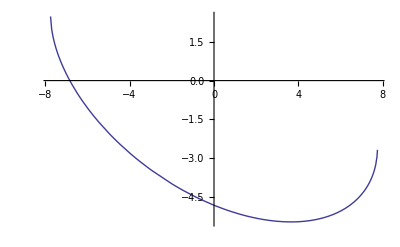

```mathematica
Plot[y/.res[[1]],{x,-100,100},PlotRange->All,AxesLabel->{"x"}]
```